```mathematica
"definição do estádio"
a=1
b=1
```

definição do estádio

1

1

```mathematica
"definição da base utilizada"
φ[x_,y_,n_,m_]=Sin[π*n((x+√(y(b-y)))/(a+2 √(y(b-y))))]Sin[π*m(y/b)]
nM=3
mM=3
Base[x_,y_]=Table[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM],{i,0,nM*mM-1}]
```

definição da base utilizada

Sin[m π y] Sin[(n π (x+√((1-y) y)))/(1+2 √((1-y) y))]

3

3

{Sin[π y] Sin[(π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[π y] Sin[(2 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[π y] Sin[(3 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[2 π y] Sin[(π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[2 π y] Sin[(2 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[2 π y] Sin[(3 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[3 π y] Sin[(π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[3 π y] Sin[(2 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[3 π y] Sin[(3 π (x+√((1-y) y)))/(1+2 √((1-y) y))]}

```mathematica
"definição da matriz A"
A[k_] =Table[NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]Laplacian[φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{x,y}],{y,0,b},{x,-√(y(b-y)),a+√(y(b-y))},AccuracyGoal->10]+k^2 NIntegrate[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{y,0,b},{x,-√(y(b-y)),a+√(y(b-y))},AccuracyGoal->10],{i,0,nM*mM-1},{j,0,nM*mM-1}]
A[k] // MatrixForm
```

definição da matriz A

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

{{-6.2063+0.481926 k^2,1.68912×10^-15-2.31208×10^-17 k^2,-0.236124+7.14639×10^-14 k^2,3.87463×10^-15-6.02265×10^-17 k^2,2.25621×10^-18+4.83631×10^-18 k^2,-2.97106×10^-15+4.48384×10^-18 k^2,0.76262-0.022303 k^2,-3.1314×10^-15-1.54841×10^-17 k^2,0.93362-3.6217×10^-13 k^2},{1.29007×10^-15-2.31208×10^-17 k^2,-10.367+0.481926 k^2,-9.94176×10^-16+4.60299×10^-17 k^2,1.55881×10^-16+4.83631×10^-18 k^2,4.19405×10^-15-5.57412×10^-17 k^2,-1.86155×10^-15-9.67318×10^-18 k^2,9.12574×10^-16-1.54841×10^-17 k^2,0.0583405-0.022303 k^2,2.1474×10^-14-2.1061×10^-16 k^2},{-0.236124+7.14639×10^-14 k^2,4.8906×10^-16+4.60299×10^-17 k^2,-17.3016+0.481926 k^2,-3.54559×10^-17+4.48384×10^-18 k^2,-6.09988×10^-16-9.67318×10^-18 k^2,1.6736×10^-14-2.50426×10^-16 k^2,-1.70784-3.6217×10^-13 k^2,1.59457×10^-14-2.1061×10^-16 k^2,-1.11546-0.022303 k^2},{1.14463×10^-15-6.02265×10^-17 k^2,-2.25621×10^-18+4.83631×10^-18 k^2,-6.38754×10^-17+4.48384×10^-18 k^2,-19.9332+0.459623 k^2,2.38084×10^-15-3.37695×10^-17 k^2,-0.623235+1.33623×10^-14 k^2,-3.75711×10^-16+3.47332×10^-17 k^2,-2.46703×10^-15+1.10166×10^-21 k^2,2.33938×10^-14-2.20857×10^-16 k^2},{9.55927×10^-17+4.83631×10^-18 k^2,1.79673×10^-15-5.57412×10^-17 k^2,-6.68373×10^-31-9.67318×10^-18 k^2,9.83372×10^-16-3.37695×10^-17 k^2,-24.7981+0.459623 k^2,1.01467×10^-14-1.54906×10^-16 k^2,-9.02483×10^-18+1.10166×10^-21 k^2,2.24754×10^-14-2.05469×10^-16 k^2,9.90421×10^-15+1.93442×10^-17 k^2},{3.29626×10^-16+4.48384×10^-18 k^2,-1.54753×10^-16-9.67318×10^-18 k^2,7.95316×10^-15-2.50426×10^-16 k^2,-0.623235+1.33623×10^-14 k^2,8.66929×10^-15-1.54906×10^-16 k^2,-32.9065+0.459623 k^2,2.62073×10^-14-2.20857×10^-16 k^2,3.60993×10^-17+1.93442×10^-17 k^2,1.25056×10^-14-3.15118×10^-17 k^2},{0.76262-0.022303 k^2,-1.84725×10^-16-1.54841×10^-17 k^2,-1.70784-3.6217×10^-13 k^2,-1.27373×10^-16+3.47332×10^-17 k^2,-6.09988×10^-16+1.10166×10^-21 k^2,1.19748×10^-14-2.20857×10^-16 k^2,-42.2967+0.453713 k^2,1.96408×10^-14-1.68531×10^-16 k^2,-0.885163+4.56776×10^-14 k^2},{-9.39169×10^-16-1.54841×10^-17 k^2,0.0583405-0.022303 k^2,8.79265×10^-15-2.1061×10^-16 k^2,4.51241×10^-18+1.10166×10^-21 k^2,1.23527×10^-14-2.05469×10^-16 k^2,-3.71408×10^-15+1.93442×10^-17 k^2,1.62928×10^-14-1.68531×10^-16 k^2,-47.5735+0.453713 k^2,-1.1003×10^-15-1.18093×10^-17 k^2},{0.93362-3.6217×10^-13 k^2,3.9682×10^-15-2.1061×10^-16 k^2,-1.11546-0.022303 k^2,1.21065×10^-14-2.20857×10^-16 k^2,3.60993×10^-17+1.93442×10^-17 k^2,2.53567×10^-15-3.15118×10^-17 k^2,-0.885163+4.56776×10^-14 k^2,-2.49489×10^-15-1.18093×10^-17 k^2,-56.3682+0.453713 k^2}}

(-6.2063+0.481926 k^2 | 1.68912×10^-15-2.31208×10^-17 k^2 | -0.236124+7.14639×10^-14 k^2 | 3.87463×10^-15-6.02265×10^-17 k^2 | 2.25621×10^-18+4.83631×10^-18 k^2 | -2.97106×10^-15+4.48384×10^-18 k^2 | 0.76262-0.022303 k^2 | -3.1314×10^-15-1.54841×10^-17 k^2 | 0.93362-3.6217×10^-13 k^2
1.29007×10^-15-2.31208×10^-17 k^2 | -10.367+0.481926 k^2 | -9.94176×10^-16+4.60299×10^-17 k^2 | 1.55881×10^-16+4.83631×10^-18 k^2 | 4.19405×10^-15-5.57412×10^-17 k^2 | -1.86155×10^-15-9.67318×10^-18 k^2 | 9.12574×10^-16-1.54841×10^-17 k^2 | 0.0583405-0.022303 k^2 | 2.1474×10^-14-2.1061×10^-16 k^2
-0.236124+7.14639×10^-14 k^2 | 4.8906×10^-16+4.60299×10^-17 k^2 | -17.3016+0.481926 k^2 | -3.54559×10^-17+4.48384×10^-18 k^2 | -6.09988×10^-16-9.67318×10^-18 k^2 | 1.6736×10^-14-2.50426×10^-16 k^2 | -1.70784-3.6217×10^-13 k^2 | 1.59457×10^-14-2.1061×10^-16 k^2 | -1.11546-0.022303 k^2
1.14463×10^-15-6.02265×10^-17 k^2 | -2.25621×10^-18+4.83631×10^-18 k^2 | -6.38754×10^-17+4.48384×10^-18 k^2 | -19.9332+0.459623 k^2 | 2.38084×10^-15-3.37695×10^-17 k^2 | -0.623235+1.33623×10^-14 k^2 | -3.75711×10^-16+3.47332×10^-17 k^2 | -2.46703×10^-15+1.10166×10^-21 k^2 | 2.33938×10^-14-2.20857×10^-16 k^2
9.55927×10^-17+4.83631×10^-18 k^2 | 1.79673×10^-15-5.57412×10^-17 k^2 | -6.68373×10^-31-9.67318×10^-18 k^2 | 9.83372×10^-16-3.37695×10^-17 k^2 | -24.7981+0.459623 k^2 | 1.01467×10^-14-1.54906×10^-16 k^2 | -9.02483×10^-18+1.10166×10^-21 k^2 | 2.24754×10^-14-2.05469×10^-16 k^2 | 9.90421×10^-15+1.93442×10^-17 k^2
3.29626×10^-16+4.48384×10^-18 k^2 | -1.54753×10^-16-9.67318×10^-18 k^2 | 7.95316×10^-15-2.50426×10^-16 k^2 | -0.623235+1.33623×10^-14 k^2 | 8.66929×10^-15-1.54906×10^-16 k^2 | -32.9065+0.459623 k^2 | 2.62073×10^-14-2.20857×10^-16 k^2 | 3.60993×10^-17+1.93442×10^-17 k^2 | 1.25056×10^-14-3.15118×10^-17 k^2
0.76262-0.022303 k^2 | -1.84725×10^-16-1.54841×10^-17 k^2 | -1.70784-3.6217×10^-13 k^2 | -1.27373×10^-16+3.47332×10^-17 k^2 | -6.09988×10^-16+1.10166×10^-21 k^2 | 1.19748×10^-14-2.20857×10^-16 k^2 | -42.2967+0.453713 k^2 | 1.96408×10^-14-1.68531×10^-16 k^2 | -0.885163+4.56776×10^-14 k^2
-9.39169×10^-16-1.54841×10^-17 k^2 | 0.0583405-0.022303 k^2 | 8.79265×10^-15-2.1061×10^-16 k^2 | 4.51241×10^-18+1.10166×10^-21 k^2 | 1.23527×10^-14-2.05469×10^-16 k^2 | -3.71408×10^-15+1.93442×10^-17 k^2 | 1.62928×10^-14-1.68531×10^-16 k^2 | -47.5735+0.453713 k^2 | -1.1003×10^-15-1.18093×10^-17 k^2
0.93362-3.6217×10^-13 k^2 | 3.9682×10^-15-2.1061×10^-16 k^2 | -1.11546-0.022303 k^2 | 1.21065×10^-14-2.20857×10^-16 k^2 | 3.60993×10^-17+1.93442×10^-17 k^2 | 2.53567×10^-15-3.15118×10^-17 k^2 | -0.885163+4.56776×10^-14 k^2 | -2.49489×10^-15-1.18093×10^-17 k^2 | -56.3682+0.453713 k^2)

```mathematica
"autovalores obtidos numericamente"
Vka=Solve[Det[A[k]]== 0 && k ≥ 0,k]
```

autovalores obtidos numericamente

{{k→3.57983},{k→4.63702},{k→5.95885},{k→6.58054},{k→7.34528},{k→8.46519},{k→9.66372},{k→10.2538},{k→11.1897}}

```mathematica
"autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia"
ka=k/.Vka[[9]]
Vc[ka]=NullSpace[A[ka]]
id=1
v=Vc[ka][[id]]
ϕ[x_,y_]=Base[x,y].v
```

autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia

11.1897

{}

1

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

{Sin[π y] Sin[(π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[π y] Sin[(2 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[π y] Sin[(3 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[2 π y] Sin[(π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[2 π y] Sin[(2 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[2 π y] Sin[(3 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[3 π y] Sin[(π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[3 π y] Sin[(2 π (x+√((1-y) y)))/(1+2 √((1-y) y))],Sin[3 π y] Sin[(3 π (x+√((1-y) y)))/(1+2 √((1-y) y))]}.{}⟦1⟧

```mathematica
"esboço da autofunção obtida"
Plot3D[ϕ[x,y],{x,-b/2,a+(b/2)},{y,0,b},RegionFunction->Function[{x,y,z},-√(y(b-y))≤ x≤a+√(y(b-y))]]
```

esboço da autofunção obtida

-Graphics3D-

curvas de nível da autofunção

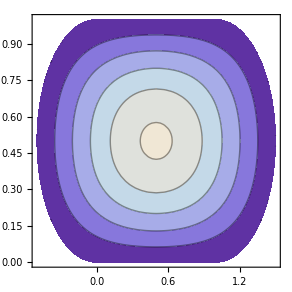

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ[x,y],{x,-b/2,a+(b/2)},{y,0,b},RegionFunction->Function[{x,y,z},-√(y(b-y))≤ x≤a+√(y(b-y))]]
```

linhas nodais da autofunção

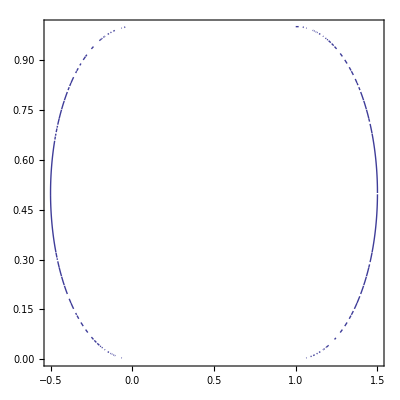

```mathematica
"linhas nodais da autofunção"
ContourPlot[ϕ[x,y]== 0,{x,-b/2,a+(b/2)},{y,0,b},RegionFunction->Function[{x,y,z},-√(y(b-y))≤ x≤a+√(y(b-y))]]
```